```mathematica
link=Install[LinkConnect["34873@192.168.150.128,35655@192.168.150.128",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωhe=1/4,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θbp=0.045,θbhe=0.0225,ωbp=15*Sqrt[0.7],ωbhe=7.5*Sqrt[0.2],ωe=150,
ωp ={0.0292,
0.1255,
0.3348,
0.5943,
0.8157,
0.9857,
1.1176,
1.2200,
1.2972,
1.3513,
1.3833,
1.3939,
1.3833,
1.3513,
1.2972,
1.2200,
1.1176,
0.9857,
0.8157,
0.5943,
0.3348,
0.1255,
0.0292},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd*2.2/2.025,vr*2.2/2.025]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe,Ωhe},{ωbp,ωe,ωbhe},{θbp,θe,θbhe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
check=With[{k=2.5,wna=86Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.03] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

DispersionKit::warn: wstpDFindRoot - root finder failed at k1 = 0.335141 and k2 = 2.7295.

{2.00716-0.0108953 ⅈ,2.00769-0.0093124 ⅈ,2.00841-0.00740441 ⅈ,2.00941-0.00492739 ⅈ,2.01089-0.00136714 ⅈ,2.01342+0.0046549 ⅈ,2.02065+0.0176133 ⅈ,2.04711+0.0315538 ⅈ,2.08221+0.0344332 ⅈ,2.11967+0.0328328 ⅈ,2.15811+0.0289988 ⅈ}

{2.00716-0.0108953 ⅈ,2.00769-0.0093124 ⅈ,2.00841-0.00740441 ⅈ,2.00941-0.00492739 ⅈ,2.01089-0.00136714 ⅈ,2.01342+0.0046549 ⅈ,2.02065+0.0176133 ⅈ,2.04711+0.0315538 ⅈ,2.08221+0.0344332 ⅈ,2.11967+0.0328328 ⅈ,2.15811+0.0289988 ⅈ,2.19691+0.0221918 ⅈ,2.23672+0.0110399 ⅈ,2.27981-0.00731572 ⅈ,2.33609-0.0404724 ⅈ}

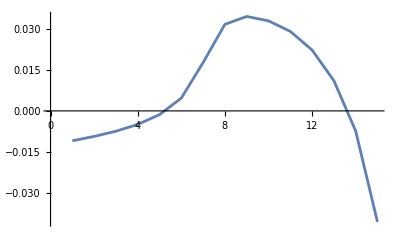

```mathematica
sol1=With[{k=Range[2.5,2.0,-0.05],wna=83Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[2.55,3.0,0.05],wna=83Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["vs=2.2,83,0.7h0.2he-0.045-im-2,2.0-3.0.csv",Im[sol]];

Export["vs=2.2,83,0.7h0.2he-0.045-re-2,2.0-3.0.csv",Re[sol]];
```